1.5

0.66

0.66

0

0.656125

0.343875

1.3787

-0.378703

40.62

50

-Graphics-

-Graphics-

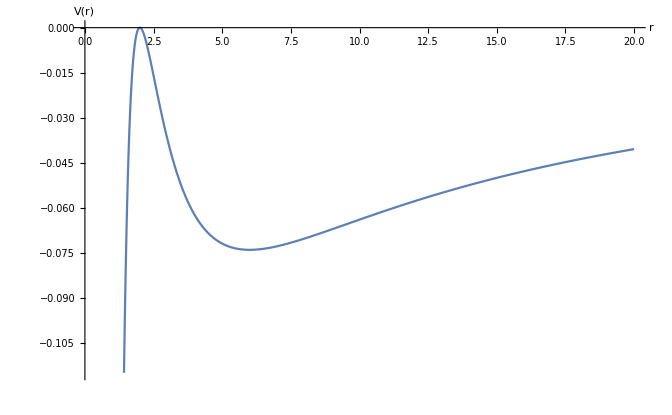

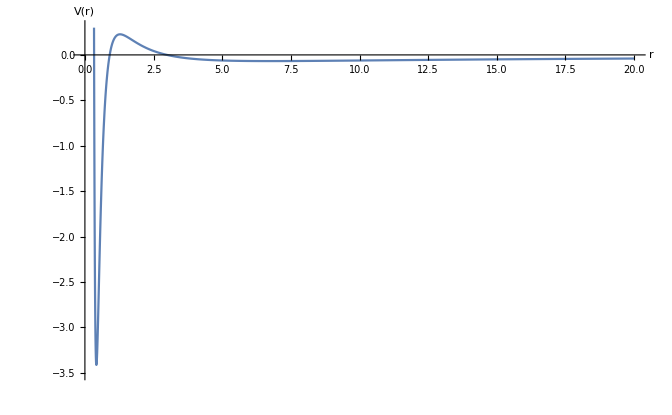

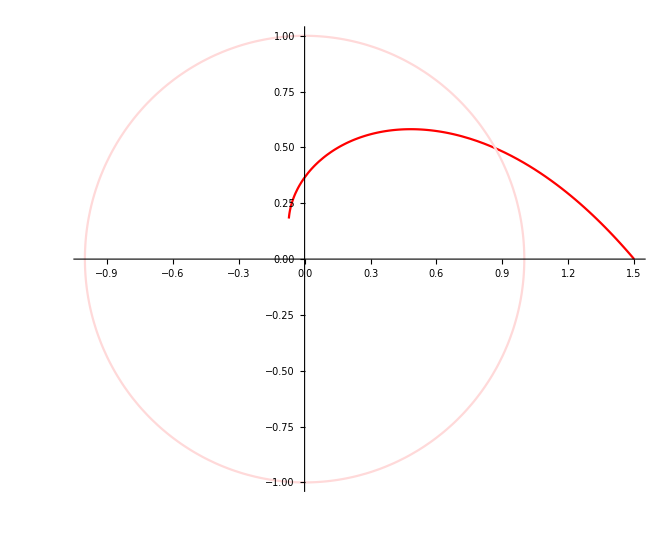

{r→InterpolatingFunction[…]}

{v→InterpolatingFunction[…]}

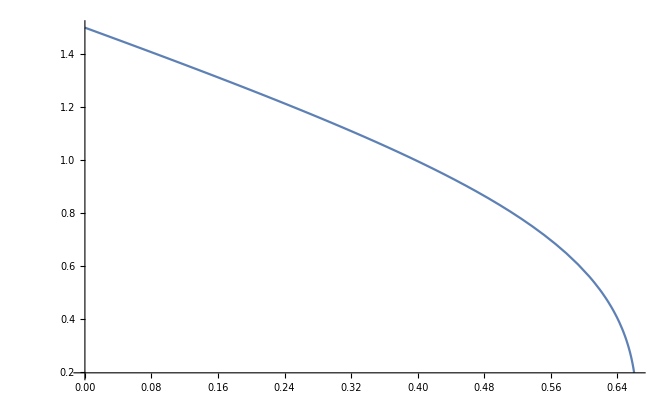

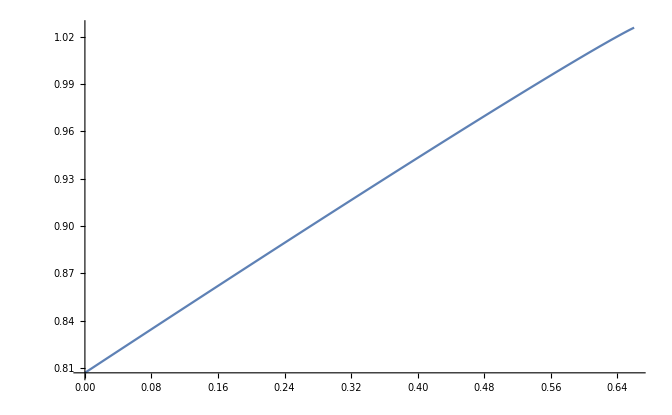

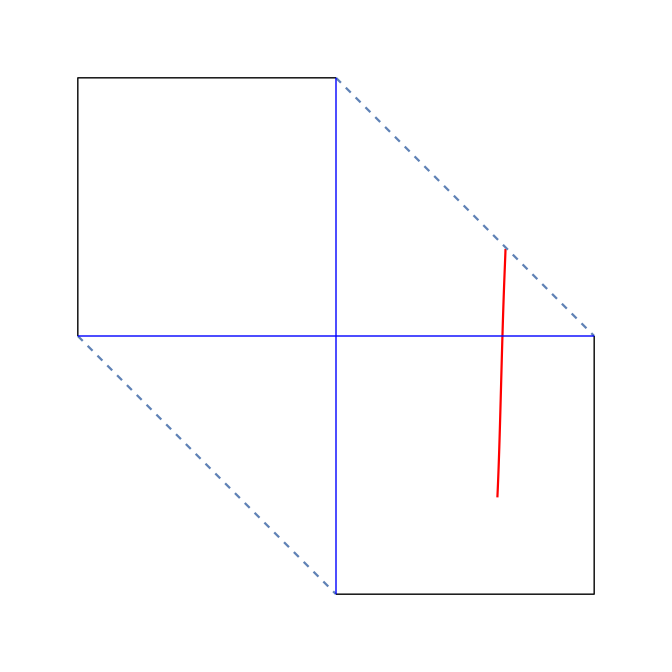

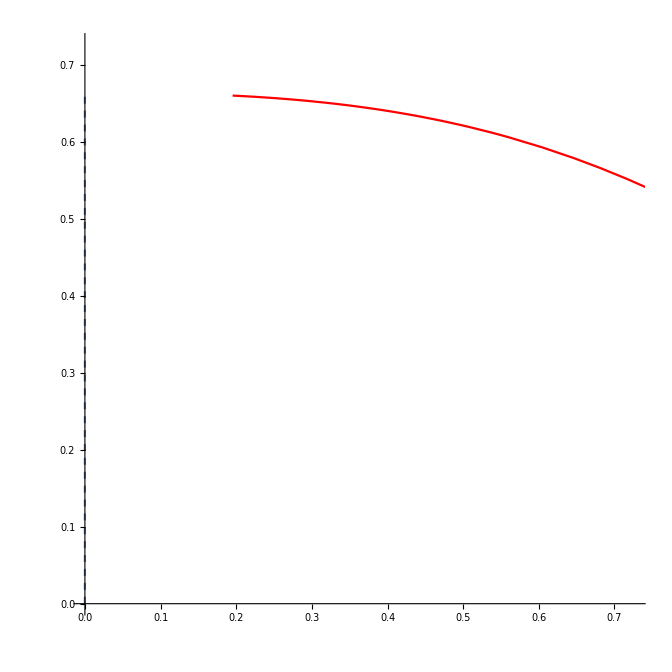

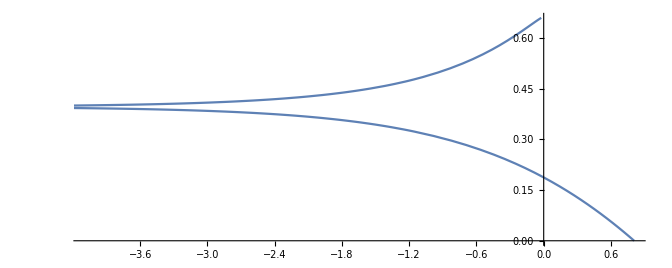

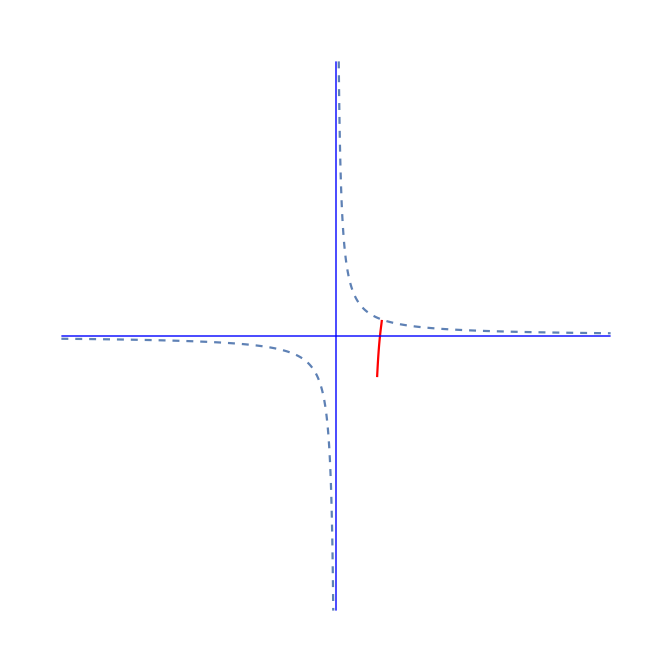

```mathematica
(*Varables*)
ε=1.5
rs= 1;
l=Sqrt[16]/2*rs;
t1= 0.66;
tP1=  0.66
tP2= 0.66
t0=0
r0=1.5*rs;
rq=0.95*rs/2;
rp=((rs/2)+Sqrt[(rs/2)^2-rq^2])
rn=((rs/2)-Sqrt[(rs/2)^2-rq^2])
ap=rp^2/(rp-rn)
an=rn^2/(rn-rp)
RNt1=40.62
RNt2=50
(**)

(*Useful functions*)
transform=CoordinateTransformData["Polar"->"Cartesian","Mapping"];
ep[r_]:=If[r<rs,1,-1];
RNep[r_]:=If[r<RNrp,1,-1];

(**)

Plot[{(Sqrt[0]/2)^2/(rr)^2-rs/(rr)-(rs*(Sqrt[0]/2)^2)/(rr)^3,(Sqrt[12]/2)^2/(rr)^2-rs/(rr)-(rs*(Sqrt[12]/2)^2)/(rr)^3,(Sqrt[24]/2)^2/(rr)^2-rs/(rr)-(rs*(Sqrt[24]/2)^2)/(rr)^3},{rr,0,50},PlotRange->{-0.8,0.4},AxesLabel->{"r","V(r)"},PlotLabels->{"l=√0 G M","l=√12 G M","l=√24 G M"}]
Plot[{(1-rs/rr+(rq^2)/rr^2)(((Sqrt[0]/2)^2)/rr^2+1)-1,(1-rs/rr+(rq^2)/rr^2)(((Sqrt[12]/2)^2)/rr^2+1)-1,(1-rs/rr+(rq^2)/rr^2)(((Sqrt[24]/2)^2)/rr^2+1)-1},{rr,0,10},PlotRange->{-5,1},AxesLabel->{"r","V(r)"},PlotLabels->{"l=√0 G M","l=√12 G M","l=√24 G M"}]
Plot[{-(1/r)+(4/(r^2))-(4/(r^3))},{r,0,20},AxesLabel->{"r","V(r)"}]
Plot[{(1-rs/r+(rq^2)/r^2)(((2)^2)/r^2+1)-1},{r,0,20},PlotRange->{-3.5,0.3},AxesLabel->{"r","V(r)"}]

(*Plot in xy *)
s1=First@NDSolve[{D[r[τ],τ]==-Sqrt[(ε^2)-(1-(rs/r[τ]))(1+l^2/r[τ]^2)],r[0]==r0},r,{τ,0,t1},MaxSteps->1000];
ϕ1[τ_]:=NIntegrate[l/(r[t]/.s1)^2,{t,0,τ}];

plot1=ParametricPlot[transform[Evaluate[{r[τ]/.s1,ϕ1[τ]}]],{τ,0,t1},PlotStyle->Red];

scr=ParametricPlot[{rs*Cos[τ],rs*Sin[τ]},{τ,0,2*Pi},PlotStyle->LightRed];

fplot=Show[plot1,scr,PlotRange->All]
(**)

(*Plot on Penrose Diagram*)
sP=First@NDSolve[{D[r[τ],τ]==-Sqrt[(ε^2)-(1-(rs/r[τ]))(1+l^2/r[τ]^2)],r[0]==r0},r,{τ,t0,tP2},MaxSteps->1000]
vP=First@NDSolve[{D[v[τ],τ]==-(Sqrt[(ε^2)-(1-(rs/(r[τ]/.sP)))]-ε)/((1-(rs/(r[τ]/.sP)))),v[0]==(r0+rs*Log[Abs[r0/rs-1]])},v,{τ,t0,tP2},MaxSteps->1000]

U=2*rs*(1-(r[τ]/.sP)/rs)*Exp[(2(r[τ]/.sP)-(v[τ]/.vP))/(2*rs)]; (*KS Coord*)
V=2*rs*1*Exp[(v[τ]/.vP)/(2*rs)]; (*KS Coord*)

pplot1=ParametricPlot[{ArcTan[V/(2rs)],ArcTan[U/(2rs)]},{τ,t0,tP2},PlotRange->{-Pi/2-0.1,Pi/2+0.1},PlotStyle->Red,Axes->False];
pplot2=ParametricPlot[{ArcTan[-V/(2rs)],ArcTan[-U/(2rs)]},{τ,t0,tP2},PlotRange->{-Pi/2-0.1,Pi/2+0.1},PlotStyle->Red,Axes->False];
pvesingplot=Plot[(Pi/2-x),{x,0,Pi/2},PlotStyle->Dashed,Axes->False]; (*singularity*)
nvesingplot=Plot[(-Pi/2-x),{x,-Pi/2,0},PlotStyle->Dashed,Axes->False]; (*singularity*)

Plot[r[τ]/.sP,{τ,0,tP2}]
Plot[v[τ]/.vP,{τ,0,tP2}]
Show[pplot1,pvesingplot,nvesingplot,Graphics[Line[{{-Pi/2,0},{-Pi/2,Pi/2},{0,Pi/2}}]],Graphics[Line[{{Pi/2,0},{Pi/2,-Pi/2},{0,-Pi/2}}]],Graphics[{RGBColor[Blue],Line[{{0,-Pi/2},{0,Pi/2}}]}],Graphics[{RGBColor[Blue],Line[{{-Pi/2,0},{Pi/2,0}}]}]]
(**)

Show[ParametricPlot[{r[τ]/.sP,τ},{τ,0,tP2},PlotStyle->Red,PlotRange->{0,tP2+(0.1*tP2)}],ParametricPlot[{rs,τ},{τ,0,tP2}],ParametricPlot[{0,τ},{τ,0,tP2},PlotStyle->Dashed,Axes->False]]
ParametricPlot[{(r[τ]/.sP)+rs Log[Abs[(r[τ]/.sP)/rs-1]],τ},{τ,0,tP2}]
Show[ParametricPlot[{V/(2*rs),U/(2*rs)},{τ,0,tP2},PlotRange->{-10,10},PlotStyle->Red,Axes->False],Plot[{1/x},{x,-10,10},PlotRange->{-10,10},PlotStyle->Dashed,Axes->False],Graphics[{RGBColor[Blue],Line[{{0,-10},{0,10}}]}],Graphics[{RGBColor[Blue],Line[{{-10,0},{10,0}}]}]]
(*(*Plot on Penrose Diagram*)
RNsP=First@NDSolve[{D[r[τ],τ]==-Sqrt[(ε^2)-((r[τ]-rn)(r[τ]-rp)/(r[τ]^2))],r[0]==r0},r,{τ,t0,tP1},MaxSteps->1000]
RNsPa=First@NDSolve[{D[r[τ],τ]==Sqrt[(ε^2)-((r[τ]-rn)(r[τ]-rp)/(r[τ]^2))],r[tP1]==Evaluate[r[tP1]/.RNsP]},r,{τ,tP1,tP2},MaxSteps->1000]
RNvP=First@NDSolve[{D[v[τ],τ]==-(Sqrt[(ε^2)-(((r[τ]/.RNsP)-rn)((r[τ]/.RNsP)-rp)/((r[τ]/.RNsP)^2))]-ε)/(((r[τ]/.RNsP)-rn)((r[τ]/.RNsP)-rp)/((r[τ]/.RNsP)^2)),v[0]==(r0+rs*Log[Abs[r0/rs-1]])},v,{τ,t0,tP1},MaxSteps->1000]
RNuP=First@NDSolve[{D[u[τ],τ]==(Sqrt[(ε^2)-(((r[τ]/.RNsPa)-rn)((r[τ]/.RNsPa)-rp)/((r[τ]/.RNsPa)^2))]-ε)/(((r[τ]/.RNsPa)-rn)((r[τ]/.RNsPa)-rp)/((r[τ]/.RNsPa)^2)),u[tP1]==Evaluate[v[tP1]/.RNvP]},u,{τ,tP1,tP2},MaxSteps->1000]


RNU=2*rs*(1-(r[τ]/.RNsP)/rs)*Exp[(2(r[τ]/.RNsP)-(v[τ]/.RNvP))/(2*rs)]; (*KS Coord*)
RNV=2*rs*1*Exp[(v[τ]/.RNvP)/(2*rs)]; (*KS Coord*)
RNUa=2*rs*(1-(r[τ]/.RNsPa)/rs)*Exp[(2(r[τ]/.RNsPa)-(u[τ]/.RNuP))/(2*rs)]; (*KS Coord*)
RNVa=2*rs*1*Exp[(u[τ]/.RNuP)/(2*rs)]; (*KS Coord*)

RN1pplot=ParametricPlot[{ArcTan[RNV/(2rs)],ArcTan[RNU/(2rs)]},{τ,t0,tP1},PlotRange->{-2Pi,2Pi},PlotStyle->Red];
RN2pplot=ParametricPlot[{ArcTan[RNVa/(2rs)],ArcTan[RNUa/(2rs)]},{τ,tP1,tP2},PlotRange->{-2Pi,2Pi},PlotStyle->{Red,Dashed}];
RNpvesingplot=Plot[(Pi/2-x),{x,0,Pi/2},PlotStyle->Dashed]; (*singularity*)
RNnvesingplot=Plot[(-Pi/2-x),{x,-Pi/2,0},PlotStyle->Dashed]; (*singularity*)

Show[RN1pplot,RN2pplot,RNpvesingplot,RNnvesingplot,Graphics[Line[{{-Pi/2,0},{-Pi/2,Pi/2},{0,Pi/2}}]],Graphics[Line[{{Pi/2,0},{Pi/2,-Pi/2},{0,-Pi/2}}]],Graphics[{Line[{{0,-Pi/2},{0,Pi/2}}],VertexColors->{Blue}}],Graphics[{Line[{{-Pi/2,0},{Pi/2,0}}],VertexColors->{Blue}}]]
(**)*)
```

```mathematica
Solve[D[-1/r+4/r^2-4/r^3,r]==0]
```

{{r→2},{r→6}}

```mathematica
-1/2+4/2^2-4/2^3
```

0

```mathematica
-1/6+4/6^2-4/6^3
```

-2/27

```mathematica
N[-2/27]
```

-0.0740741

```mathematica
((-2/27)^2)-1
```

-725/729

```mathematica
Abs[-725/729]
```

725/729

```mathematica
N[725/729]
```

0.994513

```mathematica
NumberForm[0.9945130315500685,16]
```

0.994513031550069

```mathematica
0.97^2-1
```

-0.0591

```mathematica
NumberForm[-0.01990000000000003,16]
```

-0.01990000000000003

```mathematica
Solve[D[(1-rs/rr+(rq^2)/rr^2)(((2)^2)/rr^2+1)-1,rr]==0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{rr→0.417561},{rr→1.28013},{rr→6.75356}}

```mathematica
r=6.753556918140576
0.9025/r^4-4/r^3+4.22563/r^2-1/r
```

6.75356

-0.067976

```mathematica
Sqrt[1+(0.2267)]
```

```mathematica
1.10766
```